# Atom-cavity interactions

```mathematica
constsdir="..\\constants\\";
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],constsdir}]];
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
<<"rbconsts.m"
```

## Single atom in a cavity

### Mark’s example 1 - short confocal resonator

Algebra confirmed by hand, results agree with Mark if 87 RbD1 line assumed.

```mathematica
(*CAVITY PARAMS*)
L=1.5*^-4;(*cavity length*)
RoC = L;
F =3*^4;(* (π (R1 R2)^(1/4))/(1-(R1 R2)^(1/2))cavity finesse*)
FSR = c/(2L);(*free spectral range*)
κ = 2π FSR/F; (*cavity linewidth or decay rate*)
w0 = 4.3*^-6;(*Confocal waist*)
V = (π w0^2 L)/2;(*TEM00 mode volume*)
"Cavity w0, L, F, FSR, κ/(2π): "
{w0,L,F, FSR, κ/2π}
(*ATOM PARAMS*)
d = 2.992 e a0/√2; (*D1*)
Γ = 2π 5.746*^6;(*ΓD2*); (*atom decay rate, e.g. 87Rb 5P3/2*)
λ = 7.95*^-7;(*λD2*);
"Atom d [a.u.], Γ/(2π), λ:"
{d/(e a0), Γ/(2π),λ}
(*ATOM-CAVITY INTERACTION*)
Ε = ((ℏ (2π c/λ))/(2 ϵ0 V))^(1/2);(*vacuum field strength for 1/2 photon in cavity [Hz]*)
g = d Ε/ℏ;
"Vacuum Rabi frequency g/(2π) [Hz]:"
g/(2π)
"Cooperativity, confocal [dimensionless]:"
Cooperativity = 8/(ℏ ϵ0)(d^2 F)/(Γ λ^2 L)
"Fractional emission into cavity mode:"
(2Cooperativity)/(1+2 Cooperativity)
"Quantum efficiency:"
(2Cooperativity)/(1+2Cooperativity)κ/(κ+Γ)
```

Cavity w0, L, F, FSR, κ/(2π):

{4.3×10^-6,0.00015,30000,9.99567×10^11,3.28844×10^8}

Atom d [a.u.], Γ/(2π), λ:

{2.11566,5.746×10^6,7.95×10^-7}

Vacuum Rabi frequency g/(2π) [Hz]:

4.87596×10^7

Cooperativity, confocal [dimensionless]:

24.1965

Fractional emission into cavity mode:

0.979754

Quantum efficiency:

0.835644

Compare w/ Mark’s result:

```mathematica
Cooperativity/23.9
```

1.0124

```mathematica
g/(2π 4.92*^7)
```

0.991048

### Cooperativity Trade-off

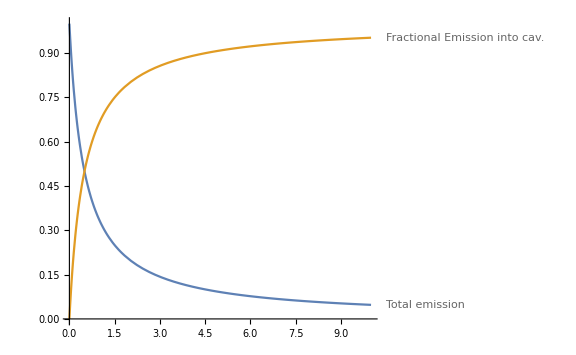

```mathematica
rTotal = 1/(1+2 coop);(*total atomic emission, Ω^2/γ = 1*)
rFrac = (2 coop)/(1+ 2 coop);(*fraction of emission into the cavity mode*)
Plot[{rTotal,rFrac},{coop,0,10},PlotLabels->{"Total emission","Fractional Emission into cav."}, ImageSize->Large]
```

## Atomic ensemble in cavity

How does the cooperativity factor change for an ensemble of atoms if we assume an effect two level state with the upper level being a W state excitation? The atomic decay rate is now enhanced, as the transition strength goes like √N for N atoms. Check this. Larger Γ_eff  -> lower cooperativity.